### Categorization

Tutorial

DoFun

DoFun`

DoFun/tutorial/Exporting diagrams

### Keywords

Details

# Exporting diagrams

The output of DSEPlot and RGEPlot looks acceptable in Mathematica, but when exporting to a pdf file, the results are sometimes unusable for presentations or articles because the indices and factors are too tiny.
Here it is explained how to improve the output to obtain acceptable results.

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

The diagrammatic representation of a simple DSE within Mathematica:

```mathematica
Needs["DoFun`"]
```

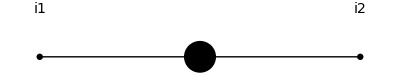
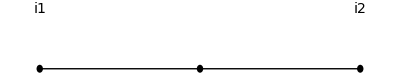
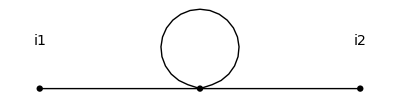
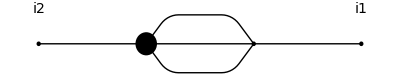
-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/6^ |

```mathematica
dse=doDSE[{{phi,4,even}},{phi,phi}];
pdse=DSEPlot[dse,{{phi,Black}}]
```

When we export the plot the indices and the factors are too tiny to be readable in a presentation or an article:

```mathematica
Export["dse.pdf",pdse];
Import["dse.pdf"]
```

{-Graphics-}

To enlarge the indices and factors we use the options factorStyle and indexStyle:

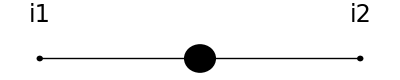
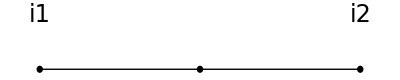
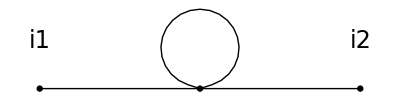
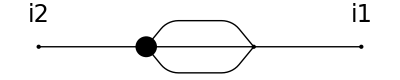
-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/6^ |

```mathematica
pdseImp=DSEPlot[dse,{{phi,Black}},factorStyle->{FontSize:>36},indexStyle->{FontSize:>24}]
```

Note that the resulting plot may not look good in Mathematica itself, but the scaling of text and diagrams is different in the pdf:

```mathematica
Export["dseImp.pdf",pdseImp];
Import["dseImp.pdf"]
```

{-Graphics-}

Another thing may disturb some people is that the indices are called i1 and i2. To denote them by i and j we have to add the corresponding arguments to the derivation of the DSE:

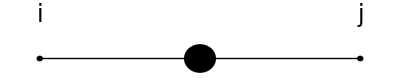
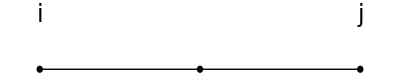
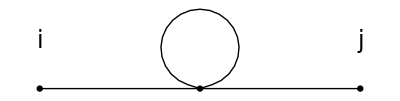
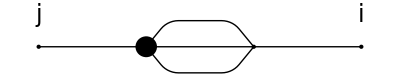
-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/6^ |

```mathematica
dseij=doDSE[{{phi,4,even}},{{phi,i},{phi,j}}];
DSEPlot[dseij,{{phi,Black}},factorStyle->{FontSize:>36},indexStyle->{FontSize:>24}]
```

If one does not use graphics primitives for the fields one can use one's own labels:

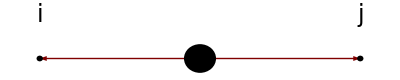
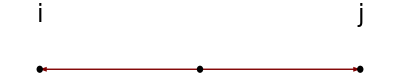
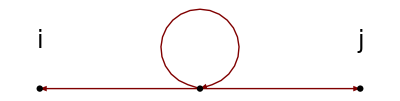
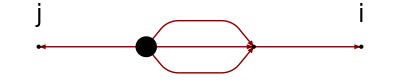
-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/6^ |

```mathematica
pdseLabels=DSEPlot[dseij,factorStyle->{FontSize:>36},indexStyle->{FontSize:>24}]/.{"phi phi leg i":>DisplayForm@StyleBox[Subscript[φ, i],FontSize->20],"phi phi leg j":>DisplayForm@StyleBox[Subscript[φ, j],FontSize->20],
"phi phi":>DisplayForm@StyleBox[D,FontSize->20]}
```

Again one should note the difference between the pdf and the Mathematica internal representation:

```mathematica
Export["dseImp2.pdf",pdseLabels];
Import["dseImp2.pdf"]
```

{-Graphics-}

More About

Related Tutorials

Related Wolfram Education Group Courses